```mathematica
Manipulate[
Module[{(*Psat1,Psat2,*)Px,Py,x1,y1,leverx},
(*Psat1=1.569;
Psat2=0.319;*)
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[P==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[P==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=(y1-0.5)/(y1-x1);

(*FindRoot[{
P==X*Psat1+(1-X)*Psat2,
P==1/(Y/Psat1+(1-Y)/Psat2),
0.5==(Y-0.5)/(Y-X)
},{
{P,1},{X,1},{Y,1}
}]*)

Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,Green}},PlotLabel->leverx]],
{{P,0.7,"P"},0.1,2,0.01,Appearance->"Labeled"},
{{Psat1,1.569,"Psat1"},1,2,0.001,Appearance->"Labeled"},
{{Psat2,0.319,"Psat2"},0.1,1,0.001,Appearance->"Labeled"}
]
```

```mathematica
(*P=0.71 Psat1=1.58 Psat2=0.319*)
(*P=0.7 Psat1=1.536 Psat2=0.319*)
```

```mathematica
90+273
150+273
```

363

423

```mathematica
4.60
1701
20.806+273
```

4.6

1701

293.806

```mathematica
4.1
1344
-53.773+273
```

4.1

1344

219.227

```mathematica
Framed[Column[{
Manipulate[
Module[{Psat1,Psat2,Pxi,Pyi,Px,Py},
Psat1[temp_]=10^(4.6-1701/(temp+293.8));
Psat2[temp_]=10^(4.1-1344/(temp+219.2));

Pxi[x_]=x*Psat1[100]+(1-x)*Psat2[100];
Pyi[x_]=(x/Psat1[100]+(1-x)/Psat2[100])^-1;
Px[x_]=x*Psat1[T]+(1-x)*Psat2[T];
Py[x_]=(x/Psat1[T]+(1-x)/Psat2[T])^-1;

Plot[{Pxi[x],Pyi[x],Px[x],Py[x]},{x,0,1},
PlotStyle->{
If[T==100,None,{Thick,Dashed,Blend[{Blue,Gray},0.5]}],
If[T==100,None,{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.5]}],
{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Frame->True,FrameLabel->{Style["mole fraction of benzene",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial",13},ImageSize->400]
],
{{T,100,"temperature (°C)"},90,150,1,Appearance->"Labeled"}
],Text@Style["Figure 10",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 10

```mathematica
FindRoot[2.05747==10^(4.6-1701/(T+293.8)),{T,10}]
FindRoot[0.431584==10^(4.1-1344/(T+219.2)),{T,10}]
```

{T→103.012}

{T→81.8122}

```mathematica
Framed[Column[{
Manipulate[
Module[{Psat1,Psat2,(*Pxi,Pyi,*)Px,Py,P,x1,y1},
Psat1[temp_]=10^(4.6-1701/(temp+293.8));
Psat2[temp_]=10^(4.1-1344/(temp+219.2));

(*Pxi[x_]=x*Psat1[100]+(1-x)*Psat2[100];
Pyi[x_]=(x/Psat1[100]+(1-x)/Psat2[100])^-1;*)

Px[x_]=x*Psat1[T]+(1-x)*Psat2[T];
Py[x_]=(x/Psat1[T]+(1-x)/Psat2[T])^-1;

P=1.7;

x1=X/.Quiet@FindRoot[Px[X]==P,{X,0.1}];
y1=Y/.Quiet@FindRoot[Py[Y]==P,{Y,0.1}];

(*p1=Plot[{Pxi[x],Pyi[x]},{x,0,1},PlotStyle->{{Thick,Dashed,Directive[Opacity[0.5,Blue]]},{Thick,Dashed,Directive[Opacity[0.5,RGBColor[0.1,0.6,0]]]}}];*)

Show[
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}}],
Graphics[{
If[Px[0.5]≥P,
{{Thick,Dashed,Blue,Line[{{x1,0},{x1,P},{0.5,P}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,P},{y1,P},{y1,0}}]}},
{Thick,Dashed,Blue,Line[{{0.5,P},{0.5,0}}]}],
{PointSize[0.02],Point[{0.5,P}]}
}],
Frame->True,FrameLabel->{Style["mole fraction of benzene",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial",13},ImageSize->400,PlotRange->{{0,1},{0.8,2.4}},Axes->False]
],
{{T,100,"temperature (°C)"},100,110,1,Appearance->"Labeled"}
],Text@Style["Figure 10",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 10

```mathematica
Framed[Column[{
Manipulate[
Module[{Psat1,Psat2,Px,Py,P,x1,y1},
Psat1[temp_]=10^(4.6-1701/(temp+293.8));
Psat2[temp_]=10^(4.1-1344/(temp+219.2));

Px[x_]=x*Psat1[T]+(1-x)*Psat2[T];
Py[x_]=(x/Psat1[T]+(1-x)/Psat2[T])^-1;

P=0.83;

x1=X/.Quiet@FindRoot[Px[X]==P,{X,0.1}];
y1=Y/.Quiet@FindRoot[Py[Y]==P,{Y,0.1}];


Show[
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}}],
Graphics[{
If[Py[0.5]≤P,
{Text[Style["liquid forms",18,FontFamily->"Arial",GrayLevel[0.5]],{0.5,1.5}],
Text[Framed@Style[Column[{Row[{"x_b = ",NumberForm[x1,2]}],Row[{"x_t = ",NumberForm[1-x1,2]}]},Alignment->"="],15,FontFamily->"Arial"],{0.27,0.87},{1,-1}],
Text[Framed[Style[Column[{Row[{"y_b = ",NumberForm[y1,2]}],Row[{"y_t = ",NumberForm[1-y1,2]}]},Alignment->"="],15,FontFamily->"Arial"],Background->White],{0.54,0.79},{-1,1}],
{Thick,Dashed,{Blue,Line[{{x1,0},{x1,P},{0.5,P}}]},{RGBColor[0.1,0.6,0],Line[{{0.5,P},{y1,P},{y1,0}}]}}
},
{Text[Framed[Style[Column[{"y_b = 0.5","y_t = 0.5"},Alignment->"="],15,FontFamily->"Arial"],Background->White],{0.54,0.79},{-1,1}],
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,P},{0.5,0}}]}
}],
{PointSize[0.02],Point[{0.5,P}]}
}],
Frame->True,FrameLabel->{Style["mole fraction of benzene",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial",13},ImageSize->400,Axes->False,PlotRange->{{0,1},{0.5,1.9}}]
],
{{T,100,"temperature (°C)"},100,90,1,Appearance->"Labeled"}
],Text@Style["Figure 10",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 10

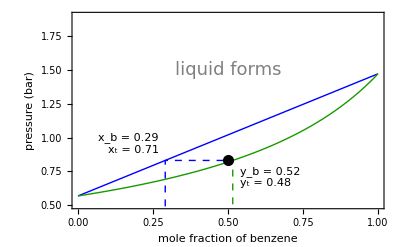
```mathematica
ImageDimensions[-Graphics-]
```

{400,262}

```mathematica
N[20.1/22.1]
```

0.909502

```mathematica
N[2/22.1]
```

0.0904977

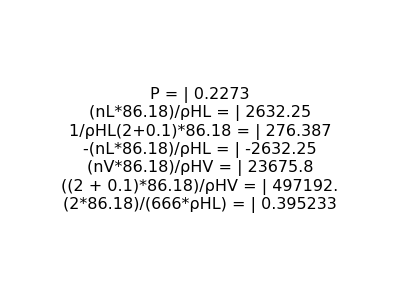

```mathematica
Module[{nL,nV,nTo,nT,zH,zi,P,Psati,PsatH,PsatO,ρHL,ρHV,vL,vV,amtL,amtV,step,Δ1,Δ2},
nL=20;
nV=0.1;
nTo=20.1;
nT=22.1;
zH=0.9095;
zi=0.0905;
P=0.2273;
Psati=If[cs==1,PsatO,PsatH];
PsatH=0.247474;
PsatO=0.024569;
ρHL=0.6548;
ρHV=3.64*^-4;
vL=2*(2632+If[cs==1,276.4*(1-step),-2632*(1-step)]);
vV=23680+If[cs==2,497200*(1-step),0];
amtL=vL/(vL+vV);
amtV=vV/(vL+vV);
step=If[cs==1,(amt-1)/0.75,(amt2-1)/0.75];
Δ1=2.75*(zi-nV);
Δ2=2.25-2.75*amtL;
Graphics[
Text[Style[Grid[{{"P =",P},{"(nL*86.18)/ρHL =",(nL*86.18)/ρHL},{"1/ρHL(2+0.1)*86.18 =",1/ρHL(2+0.1)*86.18},{"-(nL*86.18)/ρHL =",-(nL*86.18)/ρHL},{"(nV*86.18)/ρHV =",(nV*86.18)/ρHV},{"((2 + 0.1)*86.18)/ρHV =",((2+0.1)*86.18)/ρHV},{"(2*86.18)/(666*ρHL) =",(2*86.18)/(666*ρHL)}},Alignment->"="],16]
]
]
]
```

```mathematica
Framed[Column[{Manipulate[
Module[{nL,nV,nTo,nT,zH,zi,P,Psati,PsatH,PsatO,ρHL,ρHV,vL,vV,amtL,amtV,step,Δ1,Δ2,tank,piston,amounts,labels,Psat1,Psat2,plotPxy,plotlabels},
nL=20;
nV=0.1;
nTo=20.1;
nT=22.1;
zH=0.9095;
zi=0.0905;
P=0.2273;
Psati=If[cs==1,PsatO,PsatH];
PsatH=0.247474;
PsatO=0.024569;
ρHL=0.6548;
ρHV=3.64*^-4;
vL=2*(2632+If[cs==1,276.4*(1-step),-2632*(1-step)]);
vV=23680+If[cs==2,497200*(1-step),0];
amtL=vL/(vL+vV);
amtV=vV/(vL+vV);
step=If[cs==1,(amt-1)/0.75,(amt2-1)/0.75];
Δ1=2.75*(zi-nV);
Δ2=2.25-2.75*amtL;

tank=Graphics[
Inset[
Graphics3D[{
{Opacity[0.5],Cylinder[{{0,0,0},{0,0,3.25}}],Cylinder[{{1,0,1.375},{2,0,1.375}},0.12]},
{Opacity[0.75],RGBColor[0.066667,1,0.593469],Cylinder[{{0,0,0},{0,0,amtL*2.25}}],Cylinder[{{1,0,1.375},{1+0.3952*step,0,1.375}},0.12]},
Cylinder[{{1+0.3952*step,0,1.375},{2+0.3952*step,0,1.375}},0.03],
{Black,Cylinder[{{2+0.3952*step,0,1.375},{2.025+0.3952*step,0,1.375}},0.14]},
Text[Style[If[ cs==1,
If[amt==1,Row[{"2 mol ",Style["n",Italic],"-octane added"}],Row[{"add 2 mol ",Style["n",Italic],"-octane"}]],
If[amt2==1,Row[{"2 mol ",Style["n",Italic],"-hexane added"}],Row[{"add 2 mol ",Style["n",Italic],"-hexane"}]]],18,FontFamily->"Arial"],{2.15,0,1}],
{Gray,Cylinder[{{0,0,If[cs==1,2.25-Δ2*(1-step),2.25+0.5*(1-step)]},{0,0,If[cs==1,2.5-Δ2*(1-step),2.5+0.5*(1-step)]}}],Cylinder[{{0,0,If[cs==1,2.25-Δ2*(1-step),2.25+0.5*(1-step)]},{0,0,3.5}},0.12]},
If[cs==1,
If[amt==1,
{Text[Style[Row[{"2 mol ",Style["n",Italic],"-octane"}],18,FontFamily->"Arial"],{0,0,0.55*2.75*amtL}],
Text[Style[Row[{nTo," mol ",Style["n",Italic],"-hexane"}],18,FontFamily->"Arial"],{0,0,0.15*2.75*amtL}]},
{Text[Style[Column[{Row[{nL," mol ",Style["n",Italic],"-hexane"}],"liquid"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.15*2.75*amtL}],
Text[Style[Column[{Row[{nV," mol ",Style["n",Italic],"-hexane"}],"vapor"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.5*(2.75-(1-step)*(Δ2+2.75*nV+Δ1))}]}],
If[amt2==1,
{Text[Style[Row[{nTo," mol ",Style["n",Italic],"-octane"}],18,FontFamily->"Arial"],{0,0,0.55*2.75}],
Text[Style[Row[{"2 mol ",Style["n",Italic],"-hexane"}],18,FontFamily->"Arial"],{0,0,0.45*2.75}],
Text[Style["*note: volume not to scale*",14,FontFamily->"Arial"],{0,0,0.35}]},
{Text[Style[Column[{Row[{nL," mol ",Style["n",Italic],"-octane"}],"liquid"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.15*2.75*amtL*(1+(1-step))}],
Text[Style[Column[{Row[{nV," mol ",Style["n",Italic],"-octane"}],"vapor"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.5*2.75}]}]
],
Text[Style[
If[cs==1,
If[amt==1,"all vapor condenses",""],
If[amt2==1,"all liquid evaporates",""]
],18,FontFamily->"Arial"],{2.15,0,1.75}]
},Lighting->{{"Ambient",LightGray}},Boxed->False,ViewPoint->Front,PlotRange->{{-1,3.25},{-1,1},{0,3}},ImageSize->400]
],PlotRange->{{-1,3.25},{0,3}}];

plotPxy=Show[
Plot[{x*PsatH+(1-x)*PsatO,(x/PsatH+(1-x)/PsatO)^-1},{x,0,1},
Frame->True,FrameLabel->{Style[Row[{Style["n",Italic],"-hexane mole fraction"}],16],Style["pressure (bar)",16]},
LabelStyle->{Black,FontFamily->"Arial",13},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotLabel->amtL],
Graphics[{
If[cs==1,
Text[Style[If[amt<1.75,"all liquid",""],18,FontFamily->"Arial"],{0.3,0.15}],
Text[Style[If[amt2<1.75,"all vapor",""],18,FontFamily->"Arial"],{0.75,0.025}]],
If[cs==1,
{{Thick,Dashed,Line[{{1-zi*(1-step),PsatH},{1,PsatH}}]},
{PointSize[0.027],Point[{1-zi*(1-step),PsatH}]}},
{{Thick,Dashed,Line[{{0,PsatO},{zi*(1-step),PsatO}}]},
{PointSize[0.027],Point[{zi*(1-step),PsatO}]}}]
}]
];

(*Mouseover[
Show[tank,amounts,labels,ImageSize->{400,262}(*{420,320}*)],
Show[plotPxy,ImageSize->400(*{400,262}*)]
]*)
(*Grid[{
{Show[plotPxy,ImageSize->{400,282}],Show[tank,ImageSize->400]}
}]*)
Show[tank,ImageSize->400]
],
Column[{
Control[{{cs,1,"component to inject"},{1->Row[{Style["n",Italic],"-octane"}],2->Row[{Style["n",Italic],"-hexane"}]},SetterBar}],
PaneSelector[{
1->Control[{{amt,1.75,"inject isothermally"},1.75,1,0.01,Trigger,AnimationRate->1,AppearanceElements->{"PlayPauseButton","ResetButton"}}],
2->Control[{{amt2,1.75,"inject isothermally"},1.75,1,0.01,Trigger,AnimationRate->1,AppearanceElements->{"PlayPauseButton","ResetButton"}}]
},Dynamic@cs]
}]
],Text@Style["Figure 11",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 11

```mathematica
2.7
```

```mathematica
ImageDimensions[-Graphics-]
```

{400,282}

```mathematica
0.1972-0.1819
```

0.0153

```mathematica
2.5-2.35
```

0.15

```mathematica
2.75-0.15
```

2.6

```mathematica
2.6-2.35
```

0.25